```mathematica
(**1**)

h0 = 1;
h1 = 1;

a0 = 0;
a1 = 1;
a2 = 2;

fp = 2;

A =({{2h0, h0, 0}, {h0, 2(h0+h1), h1}, {0, h0, 2h0}});
B=({{3/h0(a1-a0)-3fp}, {3/h1(a2-a1)-3/h0(a1-a0)}, {3fp-3/h1(a2-a1)}});

sols=Solve[A.{c0,c1,c2}==B,{c0,c1,c2}]
```

{{c0→-3/2,c1→0,c2→3/2}}

```mathematica
a[0] = 0;
a[1] = 1;
a[2] = 2;

c[0]=-3/2;
c[1]=0;
c[2]=3/2;

h[0] = 1;
h[1] = 1;

b[j_] :=1/h[j] (a[j+1]-a[j])-h[j]/3(2c[j]+c[j+1])

b0 = b[0];
b1 = b[1];

Print["b0=",b0]
Print["b1=",b1]

d[j_]:=1/(3h[j])(c[j+1]-c[j])

d0 = d[0];
d1 = d[1];

Print["d0=",d0]
Print["d1=",d1]
```

b0=2

b1=1/2

d0=1/2

d1=1/2

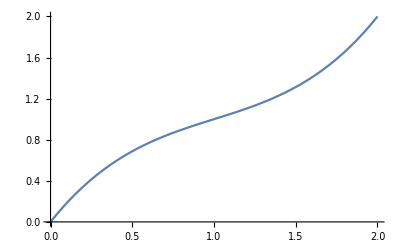

```mathematica
S0[x_]:=a[0]+b[0] x + c[0] x^2+ d[0] x^3
S1[x_]:=a[1]+b[1] (x-1) + c[1] (x-1)^2+ d[1]( x-1)^3

plots = Piecewise[{{S0[x], 0≤x≤1},{S1[x],1≤x≤2}}];

p1 =Plot[plots,{x,0,2}]
```

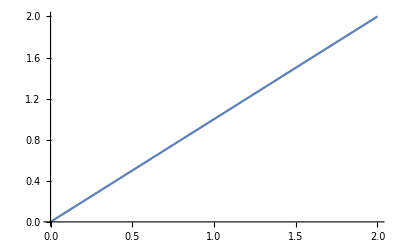

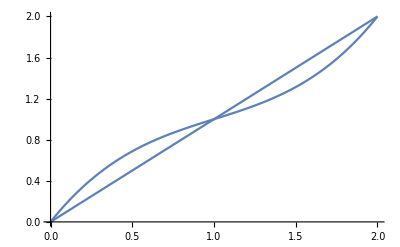

```mathematica
p2 =Plot[x,{x,0,2}]

Show[p1,p2]
```

```mathematica
(**5**)

f[x_]:=E^x

FD[h_]:=(f[h]-f[0])/h//N

For[k = 2,k≤12,k =k+2,

h = 10^-k;

y = FD[h];
Print["k=",k];
Print["f'(0)≃",y];
Print["Absolute Error =",Abs[y-f[0]]];]
```

k=2

f'(0)≃1.00502

Absolute Error =0.00501671

k=4

f'(0)≃1.00005

Absolute Error =0.0000500017

k=6

f'(0)≃1.

Absolute Error =4.99962×10^-7

k=8

f'(0)≃1.

Absolute Error =6.07747×10^-9

k=10

f'(0)≃1.

Absolute Error =8.27404×10^-8

k=12

f'(0)≃1.00009

Absolute Error =0.0000889006

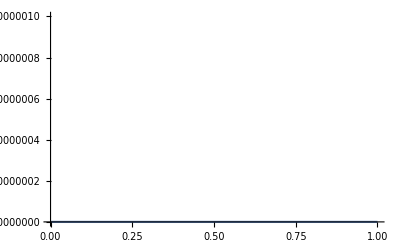

```mathematica
Plot[f[x],{x,0,.000000000001}]
```